```mathematica
SetDirectory[NotebookDirectory[]];

IsIndCopula[Copula_]:=(Copula=== "Product");

GetTestName[Copula_,Margs_]:=Module[{n=Length[Margs]},
If[IsIndCopula[Copula], "Independent",ToString[Copula[[1]]]]<>"_"<>StringTrim[ToString[Margs[[1,0]]],"Distribution"]<>"_"<>ToString[n]<>"_dim"
];

PrintResults[EstNames_,AllEsts_,AllStdDevs_,AllTimes_,AllREs_]:=Module[{},
(* Estimates. *)
Print["Estimates:"];
Do[Print["\t* ", EstNames[[e]],": ", AllEsts[[e]]],{e,Length[AllEsts]}];

(* Standard deviations. *)
Print["Standard deviations:"];
Do[Print["\t* ", EstNames[[e]],": ", AllStdDevs[[e]]],{e,Length[AllStdDevs]}];

(* Computation times. *)
Print["Times:"];
Do[Print["\t* ", EstNames[[e]],": ", AllTimes[[e]]],{e,Length[AllTimes]}];

(* Estimated relative errors. *)
Print["Estimated Relative errors:"];
Do[Print["\t* ", EstNames[[e]],": ", AllREs[[e]]],{e,Length[AllREs]}];
];

PlotResults[TestName_,ss_,EstNames_,AllEsts_,AllStdDevs_,AllTimes_,AllREs_]:=Module[{WithS,Colours,EstimatesPlotSmall,EstimatesPlotSmallSec,EstimatesPlot,StdDevsPlotSmall,SqrtWNRVPlotSmall,SqrtWNRVPlot,CombinedPlot},

WithS[Data_]:=Transpose[{ss,Data}];
Colours=Lookup["DefaultPlotStyle"]@Lookup[Method]@Charting`ResolvePlotTheme[Automatic,Plot];

EstimatesPlotSmall=
ListPlot[Map[WithS,AllEsts],Joined->True,ImageSize-> {250,125},AspectRatio->1/2,PlotRange->{{0,100}, {0,0.020}}, PlotStyle->Thickness[0.012],AxesLabel-> {"x","Estimates (Left Tail)"}];

EstimatesPlotSmallSec=
ListPlot[Map[WithS,AllEsts],Joined->True,ImageSize-> {250,125},AspectRatio->1/2,PlotRange->{{100,327},{0,0.00125}}, PlotStyle->Thickness[0.012],AxesLabel-> {"x","Estimates (Right Tail)"}];

EstimatesPlot=
ListPlot[Map[WithS,AllEsts],Joined->True,ImageSize-> {500,125},AspectRatio->0.21,PlotStyle->Thickness[0.006],AxesLabel-> {"x","Estimates"},PlotRange->{{0,20},{0,0.019}}];

StdDevsPlotSmall=
ListPlot[Map[WithS,AllStdDevs],Joined->True,PlotStyle->Thickness[0.012],AxesLabel-> {"x","Standard Deviation"},ImageSize->{250,125},PlotRange->{0,0.04},  AspectRatio->1/2];

SqrtWNRVPlotSmall=
ListPlot[Map[WithS,AllREs],Joined->True,ImageSize->{250,125},AspectRatio->1/2,PlotStyle->Thickness[0.012],AxesLabel-> {"x","Sqrt(WNRV)"},PlotRange->{0,.7}];

SqrtWNRVPlot=
ListPlot[Map[WithS,AllREs],Joined->True,ImageSize-> {500,125},AspectRatio->0.21,PlotStyle->Thickness[0.006],AxesLabel-> {"x","Sqrt(WNRV)"}];

CombinedPlot=Legended[Column[{Row[{EstimatesPlotSmall,EstimatesPlotSmallSec}],Row[{SqrtWNRVPlotSmall,StdDevsPlotSmall}]},Center],Placed[LineLegend[Colours,EstNames,LegendLayout->"Row"],Below]];

Print[TestName<>".pdf"];
Print[CombinedPlot];
Export[TestName<>".pdf",CombinedPlot];
];

PrintAndPlotResults[Copula_,Margs_,R_,ss_,PushoutEsts_,PushoutVars_,PushoutTime_,CondEsts_,CondVars_,CondTime_,AKEsts_,AKVars_,AKTime_]:=Module[{TestName,WithS,Colours,EstNames,AllEsts,AllStdDevs,AllTimes,AllREs,EstimatesPlotSmall,StdDevsPlotSmall,SqrtWNRVPlot,SqrtWNRVPlotSmall,CombinedPlot},

TestName= GetTestName[Copula,Margs];

EstNames={"Sensitivity","CondMC", "AK"};
AllEsts={PushoutEsts,CondEsts,AKEsts};
AllStdDevs=Sqrt@{PushoutVars,CondVars,AKVars};
AllTimes={PushoutTime,CondTime,AKTime};
AllREs=Quiet[Sqrt@{(PushoutTime * (PushoutVars/R)/PushoutEsts^2),(CondTime * (CondVars/R)/CondEsts^2),(AKTime * (AKVars/R)/AKEsts^2)},{Power::infy,Infinity::indet}];

PlotResults[TestName,ss,EstNames,AllEsts,AllStdDevs,AllTimes,AllREs];

Print[TestName," done"];
];
```

Frank_LogNormal_10_dim.pdf

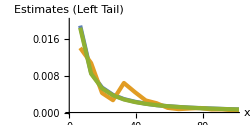
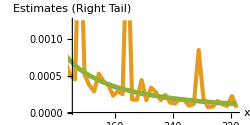
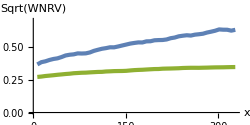
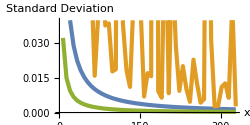

Frank_LogNormal_10_dim done

```mathematica
(* Test 4: {"Frank", 1/1000},Table[LogNormalDistribution[i-10,√i],{i,10}] *)
Copula={"Frank", 1/1000};
Margs=Table[LogNormalDistribution[i-10,√i],{i,10}];
R=10^5;
ss={6.557004003493045,13.11400800698609,19.671012010479135,26.22801601397218,32.78502001746523,39.34202402095827,45.89902802445131,52.45603202794436,59.01303603143741,65.57004003493046,72.12704403842349,78.68404804191654,85.24105204540959,91.79805604890262,98.35506005239567,104.91206405588872,111.46906805938177,118.02607206287482,124.58307606636785,131.14008006986091,137.69708407335395,144.25408807684698,150.81109208034005,157.36809608383308,163.92510008732611,170.48210409081918,177.0391080943122,183.59611209780525,190.1531161012983,196.71012010479134,203.2671241082844,209.82412811177744,216.38113211527047,222.93813611876354,229.49514012225657,236.05214412574963,242.60914812924267,249.1661521327357,255.72315613622877,262.28016013972183,268.83716414321486,275.3941681467079,281.95117215020093,288.50817615369397,295.065180157187,301.6221841606801,308.1791881641731,314.73619216766616,321.2931961711592,327.85020017465223};


PushoutEsts={0.01884544729916442,0.008608057817470722,0.005414893037344435,0.0038247645624424112,0.002916044323517639,0.002342009495289072,0.0019151958180019483,0.001596837078140324,0.0013721661140473293,0.0012045593478255147,0.0010605093071742384,0.0009586726781071669,0.0008682406504229925,0.0007811901250767218,0.0007002240332026576,0.0006375998356353998,0.0005827331612638788,0.0005387778641334992,0.0004983821600330945,0.0004685478531616483,0.0004360179140595782,0.00040594106605202013,0.0003791939128087741,0.00035467557918617026,0.0003337149670643646,0.0003157250735154186,0.00030069720193290133,0.0002828836769441329,0.0002702143493325019,0.00025539574615155575,0.00024398337535186534,0.0002339575722876967,0.00022340568205370012,0.00021154780406392005,0.00020207048311785946,0.0001916658759161217,0.00018349741057461426,0.00017632918090038273,0.00017126205212567844,0.0001637141455749557,0.00015773416738981862,0.0001522512065913,0.0001454234374051732,0.00013988344621451105,0.00013403357777170958,0.00012818637148129445,0.0001249952195742526,0.00012181158370319433,0.00011933392974385847,0.00011510123899398123};
CondEsts={0.01401727663799522,0.010730884104084897,0.004230327380065368,0.0026719378164025472,0.00640898563054623,0.004437260679792043,0.0026191919647607646,0.0020104939640597547,0.0010123194203578646,0.0007363583711856622,0.0008725646950492927,0.0009826782694154284,0.0006682684816618435,0.0006793048439197056,0.0004957492611886988,0.000450048900000729,0.002752319937148638,0.0005136068488010577,0.0003713732079558771,0.0002873626277090574,0.0005270782515019989,0.00041899737428077385,0.00037097135213814617,0.00022873665351687893,0.0002875424073765608,0.0002483248225735298,0.0025110174899735166,0.00017704884652196452,0.0001730911133733265,0.0004410394385474383,0.00016768956626629403,0.0003376021316970973,0.00027440291637216677,0.0001695662408349288,0.0002387649730568984,0.00013424497056161222,0.00012198710949999002,0.00017923481831489936,0.00016627577097138037,0.00009302724064455282,0.00011649449976697103,0.000847665315578532,0.00019833144473232879,0.00007084029866766703,0.000080981929646283,0.00015649229224992526,0.0001107995221217418,0.0000893690138958031,0.0002231083756407325,0.00006586820043409674};
AKEsts={0.018387885491355064,0.008413754013743014,0.005243590449064003,0.003727051383591903,0.0028332592177847363,0.002276501079208039,0.0018884741601730068,0.0015980762727484939,0.001373253064581042,0.00120294477610945,0.0010616610932270762,0.0009441788914269966,0.0008471211556221438,0.0007687296100211947,0.0006996612522310845,0.000641778591371041,0.0005896793382368098,0.0005455702009672583,0.0005054835447339832,0.00046989545041947083,0.00043814011239089445,0.00040980878964000356,0.0003847712606660657,0.00036310164092549763,0.0003424131465829589,0.0003236876936475691,0.00030653487562728207,0.0002912771808387477,0.00027720173274580016,0.00026340335734619744,0.00025037112550336616,0.0002390011792444047,0.0002286173219285284,0.00021848459657048463,0.00020940798065188136,0.00020073220836505233,0.00019266175660022348,0.0001849258937195701,0.00017795004815492654,0.00017121556501871693,0.00016445285762955577,0.00015840935161204786,0.0001528358381334959,0.00014761262955616746,0.00014264913198802848,0.00013774065323633896,0.00013308262505113666,0.00012878722357737374,0.00012479944006103455,0.00012066126027764444};

PushoutVars={0.13127001947266845,0.06274558231265814,0.04014429794469558,0.02909832564562602,0.02260966286517993,0.018375753394694966,0.01538429331280169,0.013190188572418245,0.011478251469627606,0.010143658348137975,0.009079126089077629,0.00818861383955493,0.007437204956742784,0.006794533573945787,0.0062488175412569605,0.005791600470513773,0.0053788035768582675,0.0050230498308987785,0.004706661454226534,0.004420970462747559,0.0041689584606456245,0.003938646391655494,0.0037310042663368202,0.0035394652631897975,0.0033611645681752085,0.003204784055944887,0.0030494714104226995,0.0029141899074579935,0.0027877572881189402,0.0026706172966919073,0.002558622309935881,0.0024565337857097376,0.002362916358613047,0.0022757778010003026,0.0021932025679618707,0.0021140435218362343,0.0020399300350603796,0.001972512595170933,0.0019079049962336273,0.0018452428565813523,0.0017874929015894337,0.0017367843670902505,0.001683741678761998,0.0016367896651644392,0.0015867444516734937,0.0015420659054105818,0.0014985952608811436,0.0014596132959614294,0.0014144026451165604,0.001378098092207798}^2;
CondVars={0.45898607487608895,0.9433324866061517,0.19134338743038468,0.06990087641287822,1.1786067545118923,0.8626965527146546,0.30830392071915436,0.2147314720552938,0.05816112263967966,0.01594452984175709,0.042437193916096995,0.06561676853718697,0.03773895525519866,0.03864179762072493,0.0178270495693036,0.018776092415722603,0.715224855295909,0.038467499411565576,0.01845254262871243,0.011107493682413762,0.048625949764803784,0.04902113264675464,0.04573488335609622,0.006927734244758473,0.01707782898114377,0.015722646203798003,0.7178262826283014,0.009279046021692086,0.006415188069293743,0.08954666320531919,0.008364343845230857,0.06851623496230719,0.028896861844280704,0.009376927765539642,0.020127361944697865,0.010180585057398451,0.004637697061619562,0.0229395544327007,0.012585911498367285,0.004279815696305354,0.0057693693134976826,0.24069931616433268,0.0316883131548763,0.00268492573223778,0.0028714296076625696,0.01113708803986169,0.012636072041925553,0.006385666665361173,0.04695286262060604,0.0026801826504486556}^2;
AKVars={0.03236451077177303,0.014964931168438927,0.009473155473174738,0.0068030576874386905,0.00522743803952723,0.004250990398208006,0.0035600241468668947,0.0030446440990388227,0.002636930202046234,0.0023381608565061635,0.002076179072749963,0.0018578227271688014,0.0016709307519174414,0.0015267126254804944,0.00139720793630537,0.0012885407342207982,0.0011861582961990955,0.0011076316356624758,0.00103016945526154,0.0009626413308534173,0.0008991948811833882,0.0008419793948494632,0.0007934980112259269,0.000755734010380566,0.0007182326393178632,0.0006823375682515818,0.0006483138532408959,0.0006197708284759046,0.0005929789848517745,0.0005662923198258919,0.0005390364940623306,0.0005181996608422442,0.0004969242136406454,0.00047571916548866665,0.00045728665114015297,0.0004396366311212694,0.0004244280355190377,0.00040842647020165483,0.000393802075124928,0.0003788605238158911,0.0003637012870530118,0.00035116666792574914,0.0003394423414140038,0.00032881559651301773,0.00031848112852200176,0.0003078460268150055,0.0002976823314209682,0.0002888075765234716,0.0002804353662069551,0.0002714137921141941}^2;

PushoutTime=274.859;
CondTime=2322.06;
AKTime=2354.48;

PrintAndPlotResults[Copula,Margs,R,ss,PushoutEsts,PushoutVars,PushoutTime,CondEsts,CondVars,CondTime,AKEsts,AKVars,AKTime]
```